# Lab 2: Functions and Lists

```mathematica
Clear["`*" ]
```

## Assignment 1: Three Slash-Dot Tasks

(a) Use slash-dot notation to figure out what this complicated expression is equal to when x is 4:  1/(3 (1+x))-(-1 + 2x)/(6 (1-x +x^2))+2/(3(1 + (1/3) (-1 +2 x)^2)).  
(b) Figure out the expression in terms of y, given x = 2y (and simplify your result)
(c) Define the following two expressions: y_1=x sin(x) and y_2=e^x. When plotted, the two curves intersect in an infinite number of places. Use FindRoot to find the intersection that occurs closest to x=0, and use slash-dot to determine what the y-value of the intersection is without doing any copying & pasting of your own.

```mathematica
1/(3 (1+x))-(-1+2x)/(6 (1-x+x^2))+2/(3(1+(1/3) (-1+2 x)^2))/.x->4
```

1/65

```mathematica
N[%]
```

0.0153846

```mathematica
1/(3 (1+x))-(-1+2x)/(6 (1-x+x^2))+2/(3(1+(1/3) (-1+2 x)^2))/.x->(2*y)
```

1/(3 (1+2 y))-(-1+4 y)/(6 (1-2 y+4 y^2))+2/(3 (1+1/3 (-1+4 y)^2))

```mathematica
Simplify[%]
```

1/(1+8 y^3)

```mathematica
y1[x_]=x*Sin[x]
```

x Sin[x]

```mathematica
y2[x_]=E^x
```

ⅇ^x

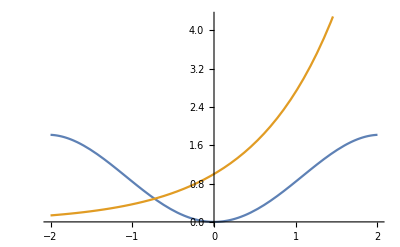

```mathematica
Plot[{y1[x],y2[x]},{x,-2,2}]
```

```mathematica
FindRoot[y1[x]==y2[x],{x,0}]
```

{x→-0.727101}

```mathematica
x/.%
```

-0.727101

```mathematica
y1[x]/.x->%
```

0.483308

## Assignment 2: Postfix and Prefix Calculations

(a) Calculate the numerical value of log(sin(sqrt(exp(7.3)))) using standard commands.
(b) Repeat, using only postfix commands.
(c) Repeat, using prefix form combined with a nameless function.

```mathematica
Log[Sin[Sqrt[Exp[7.3]]]]
```

-0.356515

```mathematica
7.3//Exp//Sqrt//Sin//Log
```

-0.356515

```mathematica
Log@Sin@Sqrt@(E^#)&@7.3
```

-0.356515

## Assignment 3: Translation to English

Type a sentence or two in standard English that describes what these commands will do (use F1 on the Exp function if you are unfamiliar with it). Then test your guess by executing the commands, and modify your sentences if needed. 
(a) Exp[q] /. q-> 2 //N   
(b) h[x_]  :=  a*Sin[x Degree]   
(c) (Sqrt[#] & )  @ {x,y,z}

(a) Take the exponential function raised to the power of “q” with “q” being 2 and do not forget to write it as a number with some decimal places.

```mathematica
Exp[q] /. q-> 2 //N
```

7.38906

(b) It will define a function h[x] when it is called later to be “a” times the sine of some input “x” times the constant pi divided by 180.

```mathematica
h[x_]  :=  a*Sin[x Degree]
```

```mathematica
h[x]/.x->0
```

0

(c) Evaluate the square root of a variable and that variable will be a list consisting of x, y, and z.

```mathematica
(Sqrt[#] & )  @ {x,y,z}
```

{√x,√y,√z}

## Assignment 4: Creating a List of Even Numbers

Use three different ways to create a list of the even numbers from 1 to 100. Each method must use a different function and just a single line of code.

```mathematica
list1=Range[2,100,2]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100}

```mathematica
list2=Table[n,{n,2,100,2}]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100}

```mathematica
list3=Array[2*#&,50]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100}

## Assignment 5: ListPlot of a Gaussian Function

Create a list of constantly-spaced points from -10 to 10, with a spacing of 0.1. Make a plot of this "Gaussian" function, e^(-x^2 /5), over that domain. Hint: Make sure you plot x-y pairs and not just a list of y-values. Doing it correctly will result in a plot centered on the origin.

```mathematica
xaxis=Range[-10,10,0.1]
```

{-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}

```mathematica
yaxis=Table[E^(-x^2/5),{x,-10,10,0.1}]
```

{2.06115×10^-9,3.06874×10^-9,4.55063×10^-9,6.72119×10^-9,9.88745×10^-9,1.44872×10^-8,2.11421×10^-8,3.07308×10^-8,4.44901×10^-8,6.41527×10^-8,9.2136×10^-8,1.31797×10^-7,1.87779×10^-7,2.66471×10^-7,3.76631×10^-7,5.30206×10^-7,7.43423×10^-7,1.03822×10^-6,1.44414×10^-6,2.00073×10^-6,2.76077×10^-6,3.79434×10^-6,5.19403×10^-6,7.08168×10^-6,9.61679×10^-6,0.0000130073,0.0000175229,0.000023512,0.0000314221,0.0000418257,0.0000554516,0.0000732231,0.0000963041,0.000126155,0.000164599,0.0002139,0.00027686,0.00035692,0.000458294,0.000586112,0.000746586,0.0009472,0.00119692,0.00150645,0.00188845,0.00235786,0.00293221,0.0036319,0.00448059,0.00550554,0.00673795,0.0082133,0.00997174,0.0120583,0.0145233,0.0174224,0.0208167,0.024773,0.0293636,0.0346659,0.0407622,0.0477393,0.0556875,0.0646996,0.0748701,0.0862936,0.0990629,0.113268,0.128993,0.146314,0.165299,0.186002,0.208462,0.232701,0.258722,0.286505,0.316004,0.347149,0.379842,0.413954,0.449329,0.48578,0.523091,0.561019,0.599296,0.637628,0.675704,0.713195,0.749762,0.785056,0.818731,0.850441,0.879853,0.906649,0.930531,0.951229,0.968507,0.982161,0.992032,0.998002,1.,0.998002,0.992032,0.982161,0.968507,0.951229,0.930531,0.906649,0.879853,0.850441,0.818731,0.785056,0.749762,0.713195,0.675704,0.637628,0.599296,0.561019,0.523091,0.48578,0.449329,0.413954,0.379842,0.347149,0.316004,0.286505,0.258722,0.232701,0.208462,0.186002,0.165299,0.146314,0.128993,0.113268,0.0990629,0.0862936,0.0748701,0.0646996,0.0556875,0.0477393,0.0407622,0.0346659,0.0293636,0.024773,0.0208167,0.0174224,0.0145233,0.0120583,0.00997174,0.0082133,0.00673795,0.00550554,0.00448059,0.0036319,0.00293221,0.00235786,0.00188845,0.00150645,0.00119692,0.0009472,0.000746586,0.000586112,0.000458294,0.00035692,0.00027686,0.0002139,0.000164599,0.000126155,0.0000963041,0.0000732231,0.0000554516,0.0000418257,0.0000314221,0.000023512,0.0000175229,0.0000130073,9.61679×10^-6,7.08168×10^-6,5.19403×10^-6,3.79434×10^-6,2.76077×10^-6,2.00073×10^-6,1.44414×10^-6,1.03822×10^-6,7.43423×10^-7,5.30206×10^-7,3.76631×10^-7,2.66471×10^-7,1.87779×10^-7,1.31797×10^-7,9.2136×10^-8,6.41527×10^-8,4.44901×10^-8,3.07308×10^-8,2.11421×10^-8,1.44872×10^-8,9.88745×10^-9,6.72119×10^-9,4.55063×10^-9,3.06874×10^-9,2.06115×10^-9}

```mathematica
combinedlist={xaxis, yaxis}//Transpose
```

{{-10.,2.06115×10^-9},{-9.9,3.06874×10^-9},{-9.8,4.55063×10^-9},{-9.7,6.72119×10^-9},{-9.6,9.88745×10^-9},{-9.5,1.44872×10^-8},{-9.4,2.11421×10^-8},{-9.3,3.07308×10^-8},{-9.2,4.44901×10^-8},{-9.1,6.41527×10^-8},{-9.,9.2136×10^-8},{-8.9,1.31797×10^-7},{-8.8,1.87779×10^-7},{-8.7,2.66471×10^-7},{-8.6,3.76631×10^-7},{-8.5,5.30206×10^-7},{-8.4,7.43423×10^-7},{-8.3,1.03822×10^-6},{-8.2,1.44414×10^-6},{-8.1,2.00073×10^-6},{-8.,2.76077×10^-6},{-7.9,3.79434×10^-6},{-7.8,5.19403×10^-6},{-7.7,7.08168×10^-6},{-7.6,9.61679×10^-6},{-7.5,0.0000130073},{-7.4,0.0000175229},{-7.3,0.000023512},{-7.2,0.0000314221},{-7.1,0.0000418257},{-7.,0.0000554516},{-6.9,0.0000732231},{-6.8,0.0000963041},{-6.7,0.000126155},{-6.6,0.000164599},{-6.5,0.0002139},{-6.4,0.00027686},{-6.3,0.00035692},{-6.2,0.000458294},{-6.1,0.000586112},{-6.,0.000746586},{-5.9,0.0009472},{-5.8,0.00119692},{-5.7,0.00150645},{-5.6,0.00188845},{-5.5,0.00235786},{-5.4,0.00293221},{-5.3,0.0036319},{-5.2,0.00448059},{-5.1,0.00550554},{-5.,0.00673795},{-4.9,0.0082133},{-4.8,0.00997174},{-4.7,0.0120583},{-4.6,0.0145233},{-4.5,0.0174224},{-4.4,0.0208167},{-4.3,0.024773},{-4.2,0.0293636},{-4.1,0.0346659},{-4.,0.0407622},{-3.9,0.0477393},{-3.8,0.0556875},{-3.7,0.0646996},{-3.6,0.0748701},{-3.5,0.0862936},{-3.4,0.0990629},{-3.3,0.113268},{-3.2,0.128993},{-3.1,0.146314},{-3.,0.165299},{-2.9,0.186002},{-2.8,0.208462},{-2.7,0.232701},{-2.6,0.258722},{-2.5,0.286505},{-2.4,0.316004},{-2.3,0.347149},{-2.2,0.379842},{-2.1,0.413954},{-2.,0.449329},{-1.9,0.48578},{-1.8,0.523091},{-1.7,0.561019},{-1.6,0.599296},{-1.5,0.637628},{-1.4,0.675704},{-1.3,0.713195},{-1.2,0.749762},{-1.1,0.785056},{-1.,0.818731},{-0.9,0.850441},{-0.8,0.879853},{-0.7,0.906649},{-0.6,0.930531},{-0.5,0.951229},{-0.4,0.968507},{-0.3,0.982161},{-0.2,0.992032},{-0.1,0.998002},{0.,1.},{0.1,0.998002},{0.2,0.992032},{0.3,0.982161},{0.4,0.968507},{0.5,0.951229},{0.6,0.930531},{0.7,0.906649},{0.8,0.879853},{0.9,0.850441},{1.,0.818731},{1.1,0.785056},{1.2,0.749762},{1.3,0.713195},{1.4,0.675704},{1.5,0.637628},{1.6,0.599296},{1.7,0.561019},{1.8,0.523091},{1.9,0.48578},{2.,0.449329},{2.1,0.413954},{2.2,0.379842},{2.3,0.347149},{2.4,0.316004},{2.5,0.286505},{2.6,0.258722},{2.7,0.232701},{2.8,0.208462},{2.9,0.186002},{3.,0.165299},{3.1,0.146314},{3.2,0.128993},{3.3,0.113268},{3.4,0.0990629},{3.5,0.0862936},{3.6,0.0748701},{3.7,0.0646996},{3.8,0.0556875},{3.9,0.0477393},{4.,0.0407622},{4.1,0.0346659},{4.2,0.0293636},{4.3,0.024773},{4.4,0.0208167},{4.5,0.0174224},{4.6,0.0145233},{4.7,0.0120583},{4.8,0.00997174},{4.9,0.0082133},{5.,0.00673795},{5.1,0.00550554},{5.2,0.00448059},{5.3,0.0036319},{5.4,0.00293221},{5.5,0.00235786},{5.6,0.00188845},{5.7,0.00150645},{5.8,0.00119692},{5.9,0.0009472},{6.,0.000746586},{6.1,0.000586112},{6.2,0.000458294},{6.3,0.00035692},{6.4,0.00027686},{6.5,0.0002139},{6.6,0.000164599},{6.7,0.000126155},{6.8,0.0000963041},{6.9,0.0000732231},{7.,0.0000554516},{7.1,0.0000418257},{7.2,0.0000314221},{7.3,0.000023512},{7.4,0.0000175229},{7.5,0.0000130073},{7.6,9.61679×10^-6},{7.7,7.08168×10^-6},{7.8,5.19403×10^-6},{7.9,3.79434×10^-6},{8.,2.76077×10^-6},{8.1,2.00073×10^-6},{8.2,1.44414×10^-6},{8.3,1.03822×10^-6},{8.4,7.43423×10^-7},{8.5,5.30206×10^-7},{8.6,3.76631×10^-7},{8.7,2.66471×10^-7},{8.8,1.87779×10^-7},{8.9,1.31797×10^-7},{9.,9.2136×10^-8},{9.1,6.41527×10^-8},{9.2,4.44901×10^-8},{9.3,3.07308×10^-8},{9.4,2.11421×10^-8},{9.5,1.44872×10^-8},{9.6,9.88745×10^-9},{9.7,6.72119×10^-9},{9.8,4.55063×10^-9},{9.9,3.06874×10^-9},{10.,2.06115×10^-9}}

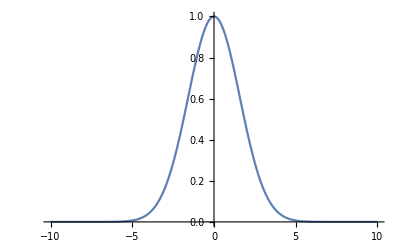

```mathematica
ListPlot[combinedlist, Joined->True]
```

## Assignment 6: A Series of List Functions

Start with list1 = {{4,8,9,10},{8,6,7,1}} and list2 = {{3,7,8,4},{3,1,2,8}}. Join the two lists together, then Flatten the resulting list, Sort in ascending order, find the Union (i.e. the unique elements), use Complement to extract only those elements that are not equal to 1, 2, or 3, Reverse the order, then finally Partition the result into pairs.  If done correctly, this exercise yields  {{10, 9}, {8, 7}, {6, 4}}.    (You'll need to read up on Join, Union, and Complement on  your own.)

```mathematica
list1 = {{4,8,9,10},{8,6,7,1}}
```

{{4,8,9,10},{8,6,7,1}}

```mathematica
list2 = {{3,7,8,4},{3,1,2,8}}
```

{{3,7,8,4},{3,1,2,8}}

```mathematica
Union[Sort[Flatten[Join[list1,list2]]]]
```

{1,2,3,4,6,7,8,9,10}

```mathematica
Partition[Reverse[Complement[%,{1,2,3}]],2]
```

{{10,9},{8,7},{6,4}}

## Assignment 7: Solving for a Vector

Let A = (3 | 2 | -4
2 | 1 | -2
4 | 2 | -5)and w = (1
2
1). Solve the matrix equation, A β = w  for the unknown vector β, and display it via MatrixForm. Hint: multiply both sides by the inverse of A.

```mathematica
A={{3,2,-4},{2,1,-2},{4,2,-5}}
```

{{3,2,-4},{2,1,-2},{4,2,-5}}

```mathematica
A//MatrixForm
```

(3 | 2 | -4
2 | 1 | -2
4 | 2 | -5)

```mathematica
w={1,2,1}
```

{1,2,1}

```mathematica
w//MatrixForm
```

(1
2
1)

```mathematica
Inverse[A].w//MatrixForm
```

(3
2
3)

## Assignment 8: How to Generate Test Data

When preparing to analyze experimental data it’s often useful to have a set of test data for testing your algorithms. To create some test data that mimics a noisy sinusoidal response, create a list of sin(x) values where x varies from x=-10 to 10 in steps of 0.1, and a list of random numbers (from -0.1 to 0.1, uniformly distributed). Then add these two lists together to create a “noisy” sin(x) function, and plot this function as a function of x (e.g. {x,function} pairs). Hint: You should have 201 values in your list.

```mathematica
sinlist=Table[Sin[x],{x,-10,10,0.1}]
```

{0.544021,0.457536,0.366479,0.271761,0.174327,0.0751511,-0.0247754,-0.124454,-0.22289,-0.319098,-0.412118,-0.501021,-0.584917,-0.662969,-0.734397,-0.798487,-0.854599,-0.902172,-0.940731,-0.96989,-0.989358,-0.998941,-0.998543,-0.988168,-0.96792,-0.938,-0.898708,-0.850437,-0.793668,-0.728969,-0.656987,-0.57844,-0.494113,-0.40485,-0.311541,-0.21512,-0.116549,-0.0168139,0.0830894,0.182163,0.279415,0.373877,0.464602,0.550686,0.631267,0.70554,0.772764,0.832267,0.883455,0.925815,0.958924,0.982453,0.996165,0.999923,0.993691,0.97753,0.951602,0.916166,0.871576,0.818277,0.756802,0.687766,0.611858,0.529836,0.44252,0.350783,0.255541,0.157746,0.0583741,-0.0415807,-0.14112,-0.239249,-0.334988,-0.42738,-0.515501,-0.598472,-0.675463,-0.745705,-0.808496,-0.863209,-0.909297,-0.9463,-0.973848,-0.991665,-0.999574,-0.997495,-0.98545,-0.963558,-0.932039,-0.891207,-0.841471,-0.783327,-0.717356,-0.644218,-0.564642,-0.479426,-0.389418,-0.29552,-0.198669,-0.0998334,0.,0.0998334,0.198669,0.29552,0.389418,0.479426,0.564642,0.644218,0.717356,0.783327,0.841471,0.891207,0.932039,0.963558,0.98545,0.997495,0.999574,0.991665,0.973848,0.9463,0.909297,0.863209,0.808496,0.745705,0.675463,0.598472,0.515501,0.42738,0.334988,0.239249,0.14112,0.0415807,-0.0583741,-0.157746,-0.255541,-0.350783,-0.44252,-0.529836,-0.611858,-0.687766,-0.756802,-0.818277,-0.871576,-0.916166,-0.951602,-0.97753,-0.993691,-0.999923,-0.996165,-0.982453,-0.958924,-0.925815,-0.883455,-0.832267,-0.772764,-0.70554,-0.631267,-0.550686,-0.464602,-0.373877,-0.279415,-0.182163,-0.0830894,0.0168139,0.116549,0.21512,0.311541,0.40485,0.494113,0.57844,0.656987,0.728969,0.793668,0.850437,0.898708,0.938,0.96792,0.988168,0.998543,0.998941,0.989358,0.96989,0.940731,0.902172,0.854599,0.798487,0.734397,0.662969,0.584917,0.501021,0.412118,0.319098,0.22289,0.124454,0.0247754,-0.0751511,-0.174327,-0.271761,-0.366479,-0.457536,-0.544021}

```mathematica
randomlist=RandomReal[{-0.1,0.1},201]
```

{-0.0601497,-0.0461567,-0.00733345,-0.0341267,-0.00516581,0.0169986,-0.0208597,0.0621255,-0.0519236,0.0586954,-0.0546979,0.0437732,0.00183725,0.0190613,0.0399055,0.0763306,0.0630239,0.0672079,-0.054564,0.0547979,-0.0251085,-0.0395151,0.046915,0.0463235,0.0744636,-0.0235089,-0.0166074,0.0861524,-0.0719248,0.0578734,0.071249,0.0796793,0.0203463,0.0722106,0.0267706,-0.0973661,-0.0363688,0.0199687,-0.0978105,-0.00954054,-0.0544004,0.0357987,0.0730065,-0.050082,-0.0213898,-0.070691,-0.0456862,-0.0196492,-0.0490959,-0.0537346,0.0127855,-0.00661915,0.0303982,0.0448198,-0.0498062,0.0790648,0.0268805,-0.0120083,-0.025956,0.0933714,0.0729689,-0.0930888,0.0926328,0.0424563,0.096273,0.080764,0.0960211,0.0974551,0.0364744,-0.0504653,0.00324771,-0.0754694,-0.0251617,0.00986418,0.0490815,-0.039173,0.0981204,-0.0648222,-0.0679983,0.0766369,0.0198073,0.0403905,-0.028176,0.034634,-0.00600573,0.0355601,-0.0173769,-0.0451573,0.0251657,-0.0060662,0.0200229,0.0427575,0.0389343,-0.00620958,-0.0433766,-0.0778871,-0.0751449,0.0520863,-0.00816169,-0.0574903,0.0788323,0.0198238,0.040958,-0.0785176,0.0264662,-0.0848773,0.0604531,0.0627995,0.039623,0.0211661,0.0300067,0.0952288,0.0720823,-0.0352309,0.0136449,-0.0296877,0.0474732,0.0957584,0.064034,-0.0451539,-0.0523208,0.0252719,-0.0599204,-0.00692878,0.0826241,-0.00176845,-0.0182564,0.00430044,0.00967765,0.022977,0.00107203,0.0645953,-0.0334637,-0.0202841,-0.0243311,0.0405118,-0.0434326,0.0925941,0.051166,0.0343381,-0.0339686,0.0110647,-0.0619922,0.0999163,0.0866421,0.0136943,-0.0185461,-0.00122555,0.0900693,0.0808852,-0.0398482,0.0333432,-0.0694984,-0.0317204,0.0378627,-0.0108544,0.0097395,0.0437971,-0.0721321,0.0987245,-0.0488359,-0.061025,-0.0931334,0.055849,0.0943268,0.00959153,-0.055684,0.0295528,-0.099814,-0.0238327,-0.077311,0.0969108,0.0853366,-0.00484234,0.0256643,-0.0758396,0.0692508,0.0507989,-0.0248601,0.0890413,0.0486005,-0.051189,-0.020934,0.00122681,0.0630704,-0.013318,0.00461625,0.0195392,0.0281146,0.077509,-0.0337702,-0.0701235,-0.0186365,0.0683396,0.0428885,-0.0592554,-0.091642,-0.065527,-0.0873125,-0.0345692,-0.0563725}

```mathematica
sinlist+randomlist
```

{0.483871,0.411379,0.359146,0.237634,0.169161,0.0921497,-0.0456351,-0.062329,-0.274813,-0.260403,-0.466816,-0.457248,-0.58308,-0.643908,-0.694492,-0.722157,-0.791575,-0.834964,-0.995295,-0.915092,-1.01447,-1.03846,-0.951628,-0.941845,-0.893456,-0.961509,-0.915316,-0.764284,-0.865593,-0.671096,-0.585738,-0.49876,-0.473767,-0.332639,-0.284771,-0.312486,-0.152918,0.00315485,-0.0147211,0.172622,0.225015,0.409675,0.537609,0.500604,0.609877,0.634849,0.727078,0.812618,0.834359,0.87208,0.97171,0.975833,1.02656,1.04474,0.943885,1.05659,0.978483,0.904158,0.84562,0.911649,0.829771,0.594677,0.704491,0.572292,0.538793,0.431547,0.351562,0.255201,0.0948485,-0.092046,-0.137872,-0.314719,-0.36015,-0.417516,-0.46642,-0.637645,-0.577343,-0.810527,-0.876495,-0.786572,-0.88949,-0.90591,-1.00202,-0.957031,-1.00558,-0.961935,-1.00283,-1.00872,-0.906873,-0.897274,-0.821448,-0.740569,-0.678422,-0.650427,-0.608019,-0.557313,-0.464563,-0.243434,-0.206831,-0.157324,0.0788323,0.119657,0.239627,0.217003,0.415885,0.394548,0.625096,0.707017,0.756979,0.804493,0.871478,0.986436,1.00412,0.928327,0.999095,0.967807,1.04705,1.08742,1.03788,0.901146,0.856977,0.888481,0.748576,0.738776,0.758087,0.596704,0.497245,0.43168,0.344666,0.262226,0.142192,0.106176,-0.0918378,-0.17803,-0.279872,-0.310271,-0.485953,-0.437242,-0.560692,-0.653428,-0.790771,-0.807212,-0.933568,-0.81625,-0.86496,-0.963836,-1.01224,-1.00115,-0.906095,-0.901567,-0.998772,-0.892471,-0.952953,-0.863988,-0.734902,-0.716395,-0.621527,-0.506888,-0.536734,-0.275152,-0.328251,-0.243187,-0.176223,0.0726629,0.210876,0.224712,0.255857,0.434403,0.394299,0.554607,0.579676,0.82588,0.879004,0.845594,0.924372,0.86216,1.03717,1.03897,0.973683,1.08798,1.03796,0.918701,0.919797,0.903399,0.917669,0.785169,0.739013,0.682508,0.613032,0.57853,0.378348,0.248975,0.204253,0.192794,0.0676639,-0.134407,-0.265969,-0.337288,-0.453792,-0.492105,-0.600394}

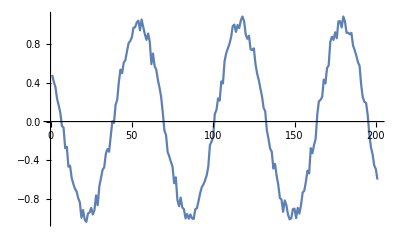

```mathematica
ListPlot[%,Joined->True]
```

## Assignment 9: Using FindRoot to Solve a Transcendental Equation...and Using the Result

Let x0 represent the value of x for which x = e^-x. It is called a transcendental equation. Determine x0 with FindRoot, and then calculate sin(x0) without using any "copy and paste"ing (i.e. use slash-dot as detailed above). Hint: when solving transcendental equations it's always good to start with a graph of the functions that represent the left and right hand sides of the equation, to give you a rough idea of the answer. The solution x0 is where the functions intersect, because that’s the place where the left and right hand sides of the equation equal each other.

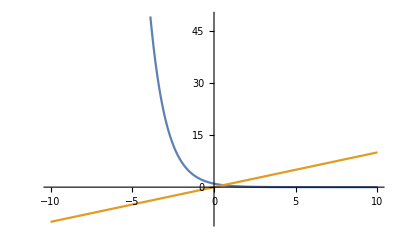

```mathematica
Plot[{E^-x,x},{x,-10,10}]
```

```mathematica
x0=FindRoot[E^-x==x,{x,0.5}]
```

{x→0.567143}

```mathematica
Sin[x/.x0]
```

0.537225

## Assignment 10: Manipulating Data

Download the file Th000088.txt into the same directory as where you have this noteboook saved. (The file is located on course website.) Open it with a text editor to see what it looks like. It contains reflectance data from a thin film of thorium taken at the Advanced Light Source at Lawrence Berkeley Labs. Then read the file into this notebook using the following Import command:

You’ll note that the data contains a header list followed by lists of four numbers.  These represent the wavelength of the beam, the measured reflected signal, and two other numbers which are not needed in this exercise.  Extract the wavelength and signal numbers and plot them using ListLogPlot.

```mathematica
SetDirectory[NotebookDirectory[]]
tdata = Import["Th000088.txt","Table"]
```

C:\Users\carte\OneDrive\Documents\Wolfram Mathematica

{{Wednesday,,November,10,,2004,11:10:02,PM},{171.934,0.00549316,-0.411987,226.93},{172.988,0.00610352,-0.411377,226.9},{174.012,0.00579834,-0.409546,226.93},{175.013,0.00701904,-0.407715,226.9},{176.016,0.00793457,-0.404053,226.9},{177.017,0.0076294,-0.401917,226.93},{178.017,0.0076294,-0.398865,226.93},{179.017,0.0076294,-0.395508,226.96},{180.015,0.0088501,-0.392761,226.9},{181.017,0.00793457,-0.38971,226.9},{182.015,0.00915527,-0.386353,226.93},{183.019,0.0088501,-0.38269,226.9},{184.02,0.010376,-0.378418,226.9},{185.014,0.00976563,-0.375366,226.9},{186.016,0.0109863,-0.372315,227.02},{187.017,0.010376,-0.367127,226.93},{188.016,0.0109863,-0.362854,226.93},{189.016,0.0125122,-0.357971,226.93},{190.016,0.0109863,-0.353394,226.87},{191.016,0.0119019,-0.348206,226.87},{192.016,0.012207,-0.343933,226.87},{193.016,0.0125122,-0.33844,226.9},{194.017,0.0128174,-0.332642,226.84},{195.016,0.0131226,-0.327148,226.9},{196.016,0.012207,-0.322571,226.9},{197.016,0.0137329,-0.317688,226.9},{198.016,0.0134277,-0.312195,226.9},{199.02,0.0128174,-0.306091,226.84},{200.02,0.0128174,-0.300293,226.87},{201.021,0.0125122,-0.293884,226.87},{202.017,0.0125122,-0.289002,226.87},{203.016,0.0134277,-0.284119,226.93},{204.015,0.0128174,-0.277405,226.84},{205.016,0.0128174,-0.270386,226.81},{206.017,0.0115967,-0.264893,226.87},{207.017,0.0119019,-0.258789,226.87},{208.017,0.0115967,-0.253906,226.84},{209.015,0.0115967,-0.247803,226.87},{210.016,0.0115967,-0.24231,226.84},{211.016,0.0119019,-0.237122,226.87},{212.016,0.0100708,-0.231323,226.81},{213.016,0.0100708,-0.22522,226.81},{214.017,0.0088501,-0.220337,226.81},{215.016,0.00976563,-0.21637,226.87},{216.017,0.0100708,-0.211792,226.84},{217.014,0.00854492,-0.206604,226.81},{218.017,0.00915527,-0.200501,226.84},{219.015,0.00732422,-0.196533,226.84},{220.016,0.00793457,-0.191345,226.87},{221.017,0.00671387,-0.187988,226.87},{222.016,0.00732422,-0.184021,226.84},{223.016,0.00732422,-0.181885,226.81},{224.016,0.00640869,-0.178528,226.84},{225.017,0.00610352,-0.175171,226.84},{226.018,0.00701904,-0.170288,226.81},{227.015,0.00518799,-0.166321,226.84},{228.016,0.00610352,-0.162964,226.84},{229.015,0.00518799,-0.159607,226.81},{230.016,0.00610352,-0.15686,226.81},{231.017,0.00488281,-0.154419,226.69},{232.016,0.00488281,-0.150757,226.81},{233.016,0.00457764,-0.149231,226.84},{234.015,0.00366211,-0.14801,226.81},{235.016,0.00549316,-0.146179,226.81},{236.019,0.00366211,-0.142822,226.81},{237.019,0.00488281,-0.13794,226.81},{238.017,0.00457764,-0.134583,226.81},{239.016,0.00396729,-0.132141,226.81},{240.016,0.00427246,-0.128784,226.81},{241.015,0.00366211,-0.126343,226.81},{242.015,0.00244141,-0.123596,226.75},{243.016,0.00366211,-0.121155,226.78},{244.018,0.00244141,-0.119324,226.78},{245.015,0.00366211,-0.116272,226.81},{246.016,0.00335693,-0.112915,226.78},{247.016,0.00427246,-0.110779,226.84},{248.016,0.00274658,-0.108643,226.84},{249.02,0.00305176,-0.105896,226.81},{250.02,0.00335693,-0.104065,226.75}}

```mathematica
Drop[tdata,1]//Transpose
Drop[%,-2]
```

{{171.934,172.988,174.012,175.013,176.016,177.017,178.017,179.017,180.015,181.017,182.015,183.019,184.02,185.014,186.016,187.017,188.016,189.016,190.016,191.016,192.016,193.016,194.017,195.016,196.016,197.016,198.016,199.02,200.02,201.021,202.017,203.016,204.015,205.016,206.017,207.017,208.017,209.015,210.016,211.016,212.016,213.016,214.017,215.016,216.017,217.014,218.017,219.015,220.016,221.017,222.016,223.016,224.016,225.017,226.018,227.015,228.016,229.015,230.016,231.017,232.016,233.016,234.015,235.016,236.019,237.019,238.017,239.016,240.016,241.015,242.015,243.016,244.018,245.015,246.016,247.016,248.016,249.02,250.02},{0.00549316,0.00610352,0.00579834,0.00701904,0.00793457,0.0076294,0.0076294,0.0076294,0.0088501,0.00793457,0.00915527,0.0088501,0.010376,0.00976563,0.0109863,0.010376,0.0109863,0.0125122,0.0109863,0.0119019,0.012207,0.0125122,0.0128174,0.0131226,0.012207,0.0137329,0.0134277,0.0128174,0.0128174,0.0125122,0.0125122,0.0134277,0.0128174,0.0128174,0.0115967,0.0119019,0.0115967,0.0115967,0.0115967,0.0119019,0.0100708,0.0100708,0.0088501,0.00976563,0.0100708,0.00854492,0.00915527,0.00732422,0.00793457,0.00671387,0.00732422,0.00732422,0.00640869,0.00610352,0.00701904,0.00518799,0.00610352,0.00518799,0.00610352,0.00488281,0.00488281,0.00457764,0.00366211,0.00549316,0.00366211,0.00488281,0.00457764,0.00396729,0.00427246,0.00366211,0.00244141,0.00366211,0.00244141,0.00366211,0.00335693,0.00427246,0.00274658,0.00305176,0.00335693},{-0.411987,-0.411377,-0.409546,-0.407715,-0.404053,-0.401917,-0.398865,-0.395508,-0.392761,-0.38971,-0.386353,-0.38269,-0.378418,-0.375366,-0.372315,-0.367127,-0.362854,-0.357971,-0.353394,-0.348206,-0.343933,-0.33844,-0.332642,-0.327148,-0.322571,-0.317688,-0.312195,-0.306091,-0.300293,-0.293884,-0.289002,-0.284119,-0.277405,-0.270386,-0.264893,-0.258789,-0.253906,-0.247803,-0.24231,-0.237122,-0.231323,-0.22522,-0.220337,-0.21637,-0.211792,-0.206604,-0.200501,-0.196533,-0.191345,-0.187988,-0.184021,-0.181885,-0.178528,-0.175171,-0.170288,-0.166321,-0.162964,-0.159607,-0.15686,-0.154419,-0.150757,-0.149231,-0.14801,-0.146179,-0.142822,-0.13794,-0.134583,-0.132141,-0.128784,-0.126343,-0.123596,-0.121155,-0.119324,-0.116272,-0.112915,-0.110779,-0.108643,-0.105896,-0.104065},{226.93,226.9,226.93,226.9,226.9,226.93,226.93,226.96,226.9,226.9,226.93,226.9,226.9,226.9,227.02,226.93,226.93,226.93,226.87,226.87,226.87,226.9,226.84,226.9,226.9,226.9,226.9,226.84,226.87,226.87,226.87,226.93,226.84,226.81,226.87,226.87,226.84,226.87,226.84,226.87,226.81,226.81,226.81,226.87,226.84,226.81,226.84,226.84,226.87,226.87,226.84,226.81,226.84,226.84,226.81,226.84,226.84,226.81,226.81,226.69,226.81,226.84,226.81,226.81,226.81,226.81,226.81,226.81,226.81,226.81,226.75,226.78,226.78,226.81,226.78,226.84,226.84,226.81,226.75}}

{{171.934,172.988,174.012,175.013,176.016,177.017,178.017,179.017,180.015,181.017,182.015,183.019,184.02,185.014,186.016,187.017,188.016,189.016,190.016,191.016,192.016,193.016,194.017,195.016,196.016,197.016,198.016,199.02,200.02,201.021,202.017,203.016,204.015,205.016,206.017,207.017,208.017,209.015,210.016,211.016,212.016,213.016,214.017,215.016,216.017,217.014,218.017,219.015,220.016,221.017,222.016,223.016,224.016,225.017,226.018,227.015,228.016,229.015,230.016,231.017,232.016,233.016,234.015,235.016,236.019,237.019,238.017,239.016,240.016,241.015,242.015,243.016,244.018,245.015,246.016,247.016,248.016,249.02,250.02},{0.00549316,0.00610352,0.00579834,0.00701904,0.00793457,0.0076294,0.0076294,0.0076294,0.0088501,0.00793457,0.00915527,0.0088501,0.010376,0.00976563,0.0109863,0.010376,0.0109863,0.0125122,0.0109863,0.0119019,0.012207,0.0125122,0.0128174,0.0131226,0.012207,0.0137329,0.0134277,0.0128174,0.0128174,0.0125122,0.0125122,0.0134277,0.0128174,0.0128174,0.0115967,0.0119019,0.0115967,0.0115967,0.0115967,0.0119019,0.0100708,0.0100708,0.0088501,0.00976563,0.0100708,0.00854492,0.00915527,0.00732422,0.00793457,0.00671387,0.00732422,0.00732422,0.00640869,0.00610352,0.00701904,0.00518799,0.00610352,0.00518799,0.00610352,0.00488281,0.00488281,0.00457764,0.00366211,0.00549316,0.00366211,0.00488281,0.00457764,0.00396729,0.00427246,0.00366211,0.00244141,0.00366211,0.00244141,0.00366211,0.00335693,0.00427246,0.00274658,0.00305176,0.00335693}}

```mathematica
%//Transpose
```

{{171.934,0.00549316},{172.988,0.00610352},{174.012,0.00579834},{175.013,0.00701904},{176.016,0.00793457},{177.017,0.0076294},{178.017,0.0076294},{179.017,0.0076294},{180.015,0.0088501},{181.017,0.00793457},{182.015,0.00915527},{183.019,0.0088501},{184.02,0.010376},{185.014,0.00976563},{186.016,0.0109863},{187.017,0.010376},{188.016,0.0109863},{189.016,0.0125122},{190.016,0.0109863},{191.016,0.0119019},{192.016,0.012207},{193.016,0.0125122},{194.017,0.0128174},{195.016,0.0131226},{196.016,0.012207},{197.016,0.0137329},{198.016,0.0134277},{199.02,0.0128174},{200.02,0.0128174},{201.021,0.0125122},{202.017,0.0125122},{203.016,0.0134277},{204.015,0.0128174},{205.016,0.0128174},{206.017,0.0115967},{207.017,0.0119019},{208.017,0.0115967},{209.015,0.0115967},{210.016,0.0115967},{211.016,0.0119019},{212.016,0.0100708},{213.016,0.0100708},{214.017,0.0088501},{215.016,0.00976563},{216.017,0.0100708},{217.014,0.00854492},{218.017,0.00915527},{219.015,0.00732422},{220.016,0.00793457},{221.017,0.00671387},{222.016,0.00732422},{223.016,0.00732422},{224.016,0.00640869},{225.017,0.00610352},{226.018,0.00701904},{227.015,0.00518799},{228.016,0.00610352},{229.015,0.00518799},{230.016,0.00610352},{231.017,0.00488281},{232.016,0.00488281},{233.016,0.00457764},{234.015,0.00366211},{235.016,0.00549316},{236.019,0.00366211},{237.019,0.00488281},{238.017,0.00457764},{239.016,0.00396729},{240.016,0.00427246},{241.015,0.00366211},{242.015,0.00244141},{243.016,0.00366211},{244.018,0.00244141},{245.015,0.00366211},{246.016,0.00335693},{247.016,0.00427246},{248.016,0.00274658},{249.02,0.00305176},{250.02,0.00335693}}

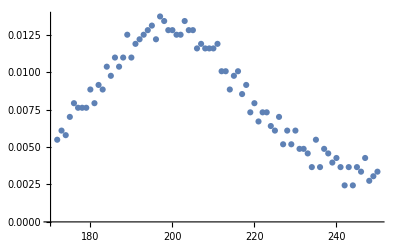

```mathematica
ListPlot[%]
```